# Minkowski Worldline with Equal Proper-Time Markers

c = 1 ly/year. Proper acceleration: +100 g for 0–10 years, −100 g for 10–20 years, then 0.

```mathematica
(*Define acceleration and solve for x(τ),t(τ) from proper time*)
Clear[x,t,eta,a,tau];
g=9.80665;                (*m/s^2*)
c=299792458;              (*m/s*)
yearSec=365.25*24*3600;   (*s/year*)
a0=.3;   (*ly/year^2 1 ly/year==c*)
ag=a0 * yearSec * c / yearSec^2 / g (*acceleration in g*)
```

0.290615

```mathematica
(*proper-acceleration profile*)
a[tau_]:=Piecewise[{{a0,0<=tau<5},{-a0,5<=tau<15},{a0,15<=tau<20}},0];
```

```mathematica
(*integrate rapidity->velocity->worldline*){xCoord,tCoord,etaFun}=NDSolveValue[{x'[tau]==Sinh[eta[tau]],t'[tau]==Cosh[eta[tau]],eta'[tau]==a[tau],x[0]==0,t[0]==0,eta[0]==0},{x,t,eta},{tau,0,25}];
```

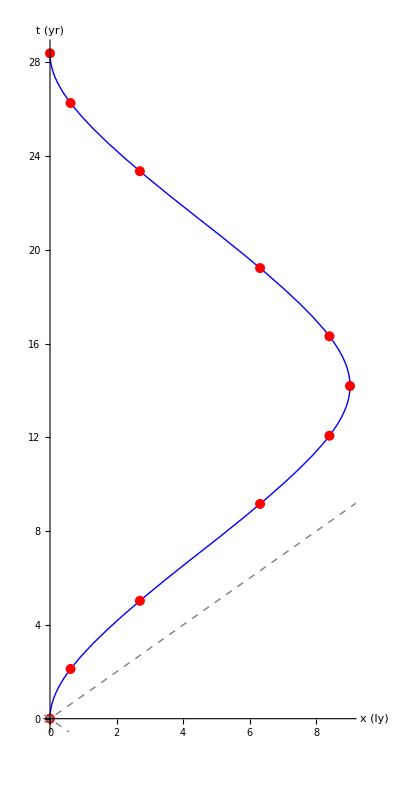

```mathematica
(*Plot worldline with equal-Δτ markers*)
Module[{Npts,tauMax,tauMarks,pts},Npts=10;
tauMax=20;(*covers both acceleration segments*)
tauMarks=Subdivide[0,tauMax,Npts];
pts={xCoord[#],tCoord[#]}&/@tauMarks;
ParametricPlot[{xCoord[tau],tCoord[tau]},{tau,0,tauMax},
PlotStyle->{Thick,Blue},
PlotRange->All,
AxesLabel->{"x (ly)","t (yr)"},
AspectRatio->2,
Epilog->{
Red,
PointSize[0.018],
Point[pts],
Gray,
PointSize[0.012],
Point[{0,0}],
Directive[Gray,Dashed],
Line[{{-30,-30},{30,30}}],
Line[{{-30,30},{30,-30}}]
}
]
]
```

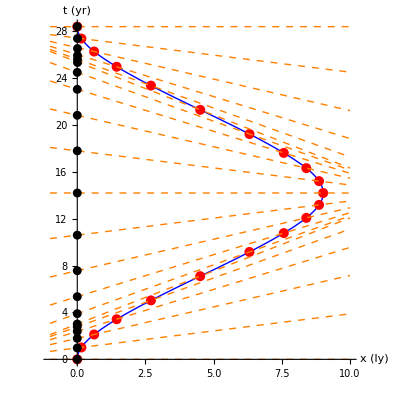

```mathematica
(* Simultaneity lines through each marker: t = v x + b, v = tanh η *)
  Module[{Npts, tauMax, tauMarks, pts, vAt, bAt, xrange, trange, worldline, simultLines},
    Npts = 20;
    tauMax = 20;
    tauMarks = Subdivide[0, tauMax, Npts];
    pts = {xCoord[#], tCoord[#]} & /@ tauMarks;

    vAt[tau_] := Tanh[etaFun[tau]];                 (* instantaneous velocity *)
    bAt[tau_] := tCoord[tau] - vAt[tau]*xCoord[tau]; (* t-axis intercept *)

    xrange = {-5, 15};
    xrange = {-1, 10};
    trange = {0, All};

    worldline = ParametricPlot[{xCoord[tau], tCoord[tau]}, {tau, 0, tauMax},
      PlotStyle -> {Thick, Blue},
      PlotRange -> {xrange, trange},
      AxesLabel -> {"x (ly)", "t (yr)"},
      AspectRatio -> 1
    ];

    simultLines = Graphics[
      Table[
        Module[{v = vAt[t], b = bAt[t], x1 = xrange[[1]], x2 = xrange[[2]]},
          {
            Directive[Orange, Dashed, Thin],
            Line[{{x1, v*x1 + b}, {x2, v*x2 + b}}],
            Black, PointSize[0.016], Point[{0, b}]  (* t-axis intersection *)
          }
        ],
        {t, tauMarks}
      ]
    ];

    Show[
      worldline,
      Graphics[{
        Red, PointSize[0.018], Point[pts]
}],
      simultLines,
      PlotRange -> {xrange, trange}
    ]
  ]
```

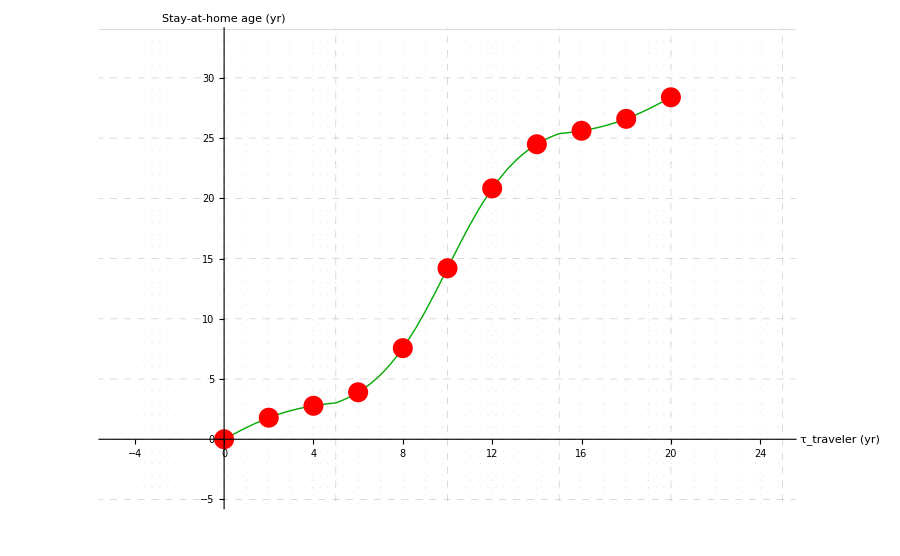

```mathematica
(* Inferred stay-at-home age vs traveler proper time, with padded axes and major/minor grids *)
  Module[{Npts, tauMax, tauMarks, vAt, bAt, inferredAge, samples, pad = 5,
          majorX, minorX, majorY, minorY},
    Npts = 10;
    tauMax = 20;
    tauMarks = Subdivide[0, tauMax, Npts];

    vAt[tau_] := Tanh[etaFun[tau]];
    bAt[tau_] := tCoord[tau] - vAt[tau]*xCoord[tau];
    inferredAge[tau_] := bAt[tau];

    samples = inferredAge /@ tauMarks;

    majorX = Range[0, tauMax + pad, 5];
    minorX = Complement[Range[0, tauMax + pad, 1], majorX];
    majorY = Range[Floor[Min[samples] - pad], Ceiling[Max[samples] + pad], 5];
    minorY = Complement[Range[Floor[Min[samples] - pad], Ceiling[Max[samples] + pad], 1], majorY];

    Plot[inferredAge[tau], {tau, 0, tauMax},
      PlotStyle -> {Thick, Darker@Green},
      PlotRange -> {{-pad, tauMax + pad}, {Min[samples] - pad, Max[samples] + pad}},
      AxesLabel -> {"τ_traveler (yr)", "Stay-at-home age (yr)"},
      GridLines -> {
        Join[({#, Directive[Gray, Dashed, Thick]} & /@ majorX),
             ({#, Directive[Gray, Dotted, Thin]} & /@ minorX)],
        Join[({#, Directive[Gray, Dashed, Thick]} & /@ majorY),
             ({#, Directive[Gray, Dotted, Thin]} & /@ minorY)]
      },
      ImageSize -> 900,
      Epilog -> {
        Red, PointSize[0.016],
        Point[Transpose[{tauMarks, samples}]]
      }
    ]
  ]
```

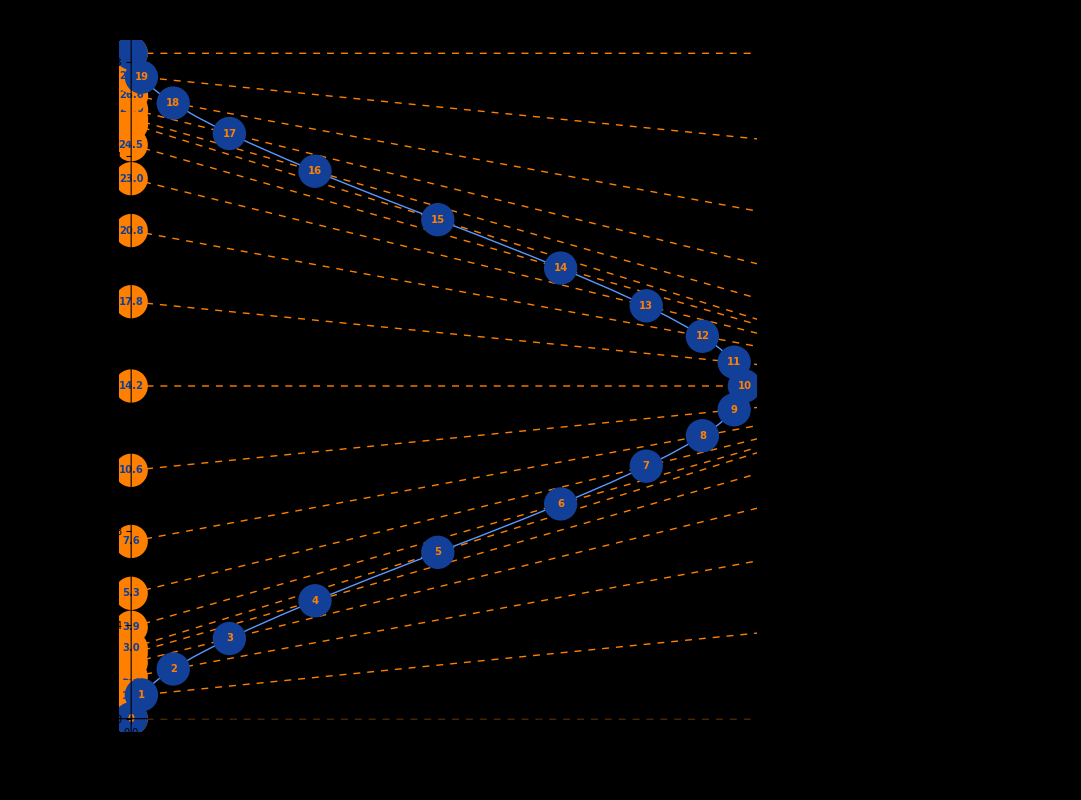
The Twin (Quasi)Paradox
-Graphics-
Proper acceleration: +0.3 ly/year^2 (≈0.29 g) for 0 ≤ τ < 5 yr; -0.3 ly/year^2 (≈ -0.29 g) for 5 ≤ τ < 15 yr; +0.3 ly/year^2 (≈0.29 g) for 15 ≤ τ < 20 yr. Units: c = 1 ly/year.

```mathematica
(* Simultaneity lines through each marker: t = v x + b, v = tanh η *)
  Module[{Npts, tauMax, tauMarks, pts, vAt, bAt, xrange, trange,
          simultPrims, tauLabels, legend, aLy = 0.3, aG = 0.2906145238716867},

    Npts = 20;
    tauMax = 20;
    tauMarks = Subdivide[0, tauMax, Npts];
    pts = {xCoord[#], tCoord[#]} & /@ tauMarks;

    vAt[tau_] := Tanh[etaFun[tau]];
    bAt[tau_] := tCoord[tau] - vAt[tau]*xCoord[tau];

    xrange = {-1, 10};
    trange = {0, All};

    simultPrims = Table[
      Module[{v = vAt[t], b = bAt[t], x1 = xrange[[1]], x2 = xrange[[2]]},
        {
          Directive[Orange, Dashed, Thin],
          Line[{{x1, v*x1 + b}, {x2, v*x2 + b}}],
          Orange, PointSize[0.03], Point[{0, b}],
          Text[Style[NumberForm[b, {4, 1}], DarkBlue, 10, Bold], {0, b}, {0, 0}]
        }
      ],
      {t, tauMarks}
    ];

    tauLabels = MapThread[
      Text[Style[NumberForm[#1, {4, 1}], Orange, 10, Bold], #2, {0, 0}] &,
      {tauMarks, pts}
    ];

    legend = Placed[
      SwatchLegend[
        {
          Directive[RGBColor[0.35, 0.6, 1], Thick],
          Directive[DarkBlue, PointSize[0.03]],
          Directive[Orange, Dashed, Thin],
          Directive[Orange, PointSize[0.03]]
        },
        {
          "Traveler worldline",
          "Equal Δτ markers (1 yr)",
          "Simultaneity line (traveler's “now”)",
          "t-axis intercept = stay-at-home age"
        },
        LegendMarkers -> {
          {Graphics[{Line[{{0, 0}, {1, 0}}]}], 30},
          {Graphics[{Disk[]}], 16},
          {Graphics[{Dashing[{Small, Small}], Line[{{0, 0}, {1, 0}}]}], 30},
          {Graphics[{Disk[]}], 16}
        },
        LabelStyle -> Directive[FontSize -> 14],
        LegendFunction -> (Framed[#, Background -> Black, FrameStyle -> Gray, FrameMargins -> 10] &)
      ],
      {Right, 0.9}
    ];

    Panel[
      Column[
        {
          Style["The Twin (Quasi)Paradox", White, 22, Bold],
          Legended[
            ParametricPlot[{xCoord[tau], tCoord[tau]}, {tau, 0, tauMax},
              PlotStyle -> {Thick, RGBColor[0.35, 0.6, 1]},
              PlotRange -> {xrange, trange},
              AxesLabel -> {"x (ly)", "t (yr)"},
              BaseStyle -> Directive[FontSize -> 16],
              AspectRatio -> 1,
              ImageSize -> 800,
              Prolog -> simultPrims,
              Epilog -> {DarkBlue, PointSize[0.03], Point[pts], tauLabels},
              Background -> Black
            ],
            legend
          ],
          Style[
            Row[{
              "Proper acceleration: +", aLy, " ly/year^2 (≈", NumberForm[aG, {3, 2}], " g) for 0 ≤ τ < 5 yr; ",
              "-", aLy, " ly/year^2 (≈ -", NumberForm[aG, {3, 2}], " g) for 5 ≤ τ < 15 yr; ",
              "+", aLy, " ly/year^2 (≈", NumberForm[aG, {3, 2}], " g) for 15 ≤ τ < 20 yr. ",
              "Units: c = 1 ly/year."
            }],
            White, 14, LineSpacing -> {1.2, 0}
          ]
        },
        Alignment -> Center,
        Spacings -> {Automatic, 0.6}
      ],
      Background -> Black,
      FrameMargins -> 10
    ]
  ]
```

```mathematica
(* Simultaneity lines through each marker: t = v x + b, v = tanh η *)
  Module[{Npts, tauMax, tauMarks, pts, vAt, bAt, xrange, trange,
          simultPrims, tauLabels, legend,
          aLy = 0.3, aG = 0.2906145238716867,
          homeAge, deltaAge},

    Npts = 20;
    tauMax = 20;
    tauMarks = Subdivide[0, tauMax, Npts];
    pts = {xCoord[#], tCoord[#]} & /@ tauMarks;

    vAt[tau_] := Tanh[etaFun[tau]];
    bAt[tau_] := tCoord[tau] - vAt[tau]*xCoord[tau];

    xrange = {-1, 10};
    trange = {0, All};

    (* inferred stay-at-home age at final τ *)
    homeAge = bAt[tauMax];
    deltaAge = homeAge - tauMax;

    simultPrims = Table[
      Module[{v = vAt[t], b = bAt[t], x1 = xrange[[1]], x2 = xrange[[2]]},
        {
          Directive[Orange, Dashed, Thin],
          Line[{{x1, v*x1 + b}, {x2, v*x2 + b}}],
          Orange, PointSize[0.03], Point[{0, b}],
          Text[Style[NumberForm[b, {4, 1}], DarkBlue, 10, Bold], {0, b}, {0, 0}]
        }
      ],
      {t, tauMarks}
    ];

    tauLabels = MapThread[
      Text[Style[NumberForm[#1, {4, 1}], Orange, 10, Bold], #2, {0, 0}] &,
      {tauMarks, pts}
    ];

    legend = Placed[
      SwatchLegend[
        {
          Directive[RGBColor[0.35, 0.6, 1], Thick],
          Directive[DarkBlue, PointSize[0.03]],
          Directive[Orange, Dashed, Thin],
          Directive[Orange, PointSize[0.03]]
        },
        {
          "Traveler worldline",
          "Equal Δτ markers (1 yr)",
          "Simultaneity line (traveler's “now”)",
          "t-axis intercept = stay-at-home age"
        },
        LegendMarkers -> {
          {Graphics[{Line[{{0, 0}, {1, 0}}]}], 30},
          {Graphics[{Disk[]}], 16},
          {Graphics[{Dashing[{Small, Small}], Line[{{0, 0}, {1, 0}}]}], 30},
          {Graphics[{Disk[]}], 16}
        },
        LabelStyle -> Directive[FontSize -> 14],
        LegendFunction -> (Framed[#, Background -> Black, FrameStyle -> Gray, FrameMargins -> 10] &)
      ],
      {Right, 0.9}
    ];

    Panel[
      Column[
        {
          Style["The Twin (Quasi)Paradox", White, 22, Bold],
          Legended[
            ParametricPlot[{xCoord[tau], tCoord[tau]}, {tau, 0, tauMax},
              PlotStyle -> {Thick, RGBColor[0.35, 0.6, 1]},
              PlotRange -> {xrange, trange},
              AxesLabel -> {"x (ly)", "t (yr)"},
              BaseStyle -> Directive[FontSize -> 16],
              AspectRatio -> 1,
              ImageSize -> 800,
              Prolog -> simultPrims,
              Epilog -> {DarkBlue, PointSize[0.03], Point[pts], tauLabels},
              Background -> Black
            ],
            legend
          ],
          Column[
            {
              Style["Traveler's proper time τ (their clock) vs stay-at-home inertial time t.", White, 14],
              Style["Trajectory: accelerate out, flip, then return while decelerating/accelerating.", White, 14],
              Style[
                Column[{
                  Row[{"0 ≤ τ < 5 yr: +", aLy, " ly/", Superscript["year", 2], " (≈ ", NumberForm[aG, {3, 2}], " g)"}],
                  Row[{"5 ≤ τ < 15 yr: -", aLy, " ly/", Superscript["year", 2], " (≈ -", NumberForm[aG, {3, 2}], " g)"}],
                  Row[{"15 ≤ τ < 20 yr: +", aLy, " ly/", Superscript["year", 2], " (≈ ", NumberForm[aG, {3, 2}], " g)"}]
                },
                Spacings -> 0.2],
                White, 14
              ],
              Style[
                Row[{
                  "At τ = ", tauMax, " yr, stay-at-home age from simultaneity: ",
                  NumberForm[homeAge, {5, 2}], " yr (older by ", NumberForm[deltaAge, {4, 2}], " yr)."
                }],
                White, 14
              ]
            },
            Alignment -> Center,
            Spacings -> 0.4
          ]
        },
        Alignment -> Center,
        Spacings -> {Automatic, 0.6}
      ],
      Background -> Black,
      FrameMargins -> 10
    ]
  ]
```

The Twin (Quasi)Paradox
-Graphics-
Traveler's proper time τ (their clock) vs stay-at-home inertial time t.
Trajectory: accelerate out, flip, then return while decelerating/accelerating.
0 ≤ τ < 5 yr: +0.3 ly/year^2 (≈ 0.29 g)
5 ≤ τ < 15 yr: -0.3 ly/year^2 (≈ -0.29 g)
15 ≤ τ < 20 yr: +0.3 ly/year^2 (≈ 0.29 g)
At τ = 20 yr, stay-at-home age from simultaneity: 28.39 yr (older by 8.39 yr).